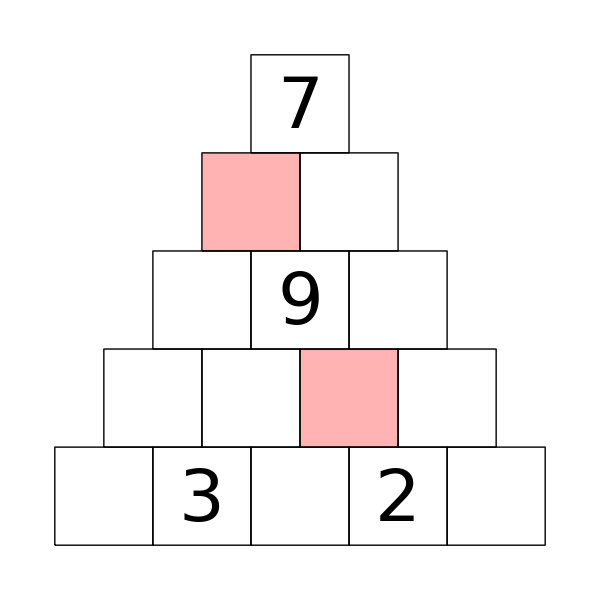
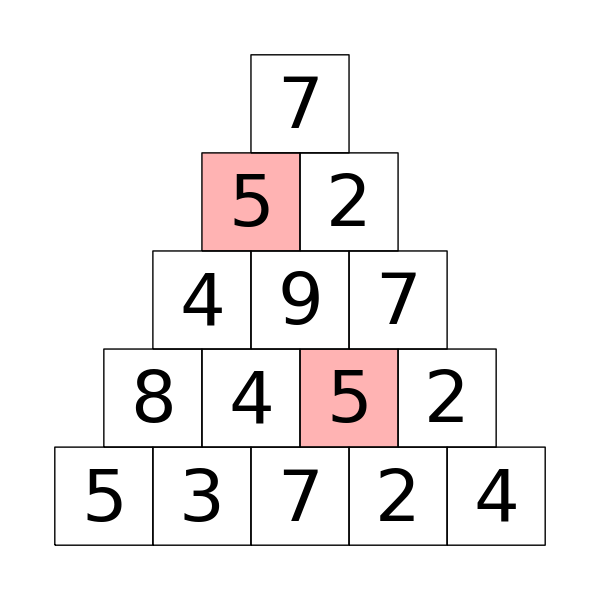

```mathematica
s[x_,y_]:=Line[{{x,y},{x+1,y},{x+1,y+1},{x,y+1},{x,y}}]
```

```mathematica
grid[n_]:=Table[s[j+i/2,i],{i,1,n},{j,1,n+1-i}]
```

```mathematica
showgiven[L_]:=Map[Text[Style[#[[2]],FontSize->20],{#[[1,2]]+#[[1,1]]/2+1/2,#[[1,1]]+1/2-.05}]&,L]
```

```mathematica
showall[L_]:=MapIndexed[Text[Style[#1,FontSize->20],{#2[[2]]+#2[[1]]/2+1/2,#2[[1]]+1/2-.05}]&,L,{2}]
```

```mathematica
modify[{x_,y_}]:=(r=RandomReal[];Which[r<1/3,{x+1,y},r<2/3,{x,y+1},True,{x,y}])
```

```mathematica
pic[M_:{}]:=Style[Show[Graphics[{MapIndexed[{col[[#2[[1]]]],Rectangle[{#1[[1,2]]+#1[[1,1]]/2,#1[[1,1]]}],Rectangle[{#1[[2,2]]+#1[[2,1]]/2,#1[[2,1]]}]}&,M],grid[n],showgiven[given]}],ImageSize->25n],Antialiasing->False]
```

```mathematica
fullpic[L_,M_:{}]:=Style[Show[Graphics[{MapIndexed[{col[[#2[[1]]]],Rectangle[{#1[[1,2]]+#1[[1,1]]/2,#1[[1,1]]}],Rectangle[{#1[[2,2]]+#1[[2,1]]/2,#1[[2,1]]}]}&,M],grid[n],showall[L]}],ImageSize->25n],Antialiasing->False]
```

```mathematica
col={Hue[0,.3],Hue[.55,.3],Hue[.17,.3],Hue[.8,.3]};
```

```mathematica
pic[]
```

-Graphics-

```mathematica
nearby[{x1_,y1_},{x2_,y2_}]:=(Abs[x1-x2]>1||Abs[y1-y2]>1||(x1-x2==y1-y2&&{x1,y1}=!={x2,y2}))
```

```mathematica
create:=Module[{top,pos1,pos2,possible,t1,t2,t3,star,low,lower,lowest,temp,res},
given={{modify[{1,1}],RandomInteger[{1,9}]},{modify[{n-1,1}],RandomInteger[{1,9}]},{modify[{1,n-1}],RandomInteger[{1,9}]}};
star=ReplacePart[Table[0,{i,1,n},{j,1,n+1-i}],Map[#[[1]]->#[[2]]&,given]];
stac={star};
While[Count[stac[[1]],0,Infinity]>0,
top=stac[[1]];
stac=Rest[stac];
{pos1,pos2}=Position[top,0][[1]];
If[pos1==1,possible=Range[1,9],
t1=top[[pos1-1,pos2]];
t2=top[[pos1-1,pos2+1]];
possible=Select[{Abs[t1-t2],t1+t2},1≤#≤9&]];
If[pos2>1,t2=top[[pos1,pos2-1]];t3=top[[pos1+1,pos2-1]];
If[t3>0,possible=Intersection[possible,{t2+t3,t2-t3,t3-t2}]]];
stac=stac~Join~Map[ReplacePart[top,{pos1,pos2}->#]&,possible];
If[stac=={},Break[]]];
(*Print["stack=",Length[stac]];*)
If[Length[stac]>0,
res={};old=Infinity;
While[old>Length[stac]>1,
old=Length[stac];low=Infinity;lowest={};lower={0};
For[i1=1,i1≤n,i1++,
For[j1=1,j1≤n+1-i1,j1++,
If[star[[i1,j1]]==0&&Not[MemberQ[Flatten[res,1],{i1,j1}]],
For[i2=i1,i2≤n,i2++,
For[j2=1,j2≤n+1-i2,j2++,
If[star[[i2,j2]]==0&&Not[MemberQ[Flatten[res,1],{i2,j2}]]&&((Abs[i1-i2]>1)||(Abs[j1-j2]>1)||(i1-i2==j1-j2)),
temp=Select[stac,#[[i1,j1]]==#[[i2,j2]]&];
If[0<Length[temp]<low,low=Length[temp];lower=temp;lowest={{i1,j1},{i2,j2}}]]]]]]];
stac=lower;
AppendTo[res,lowest];
(*Print["stack=",Length[stac]]*)];
If[Length[stac]==1&&Not[Apply[And,Map[EvenQ,Flatten[stac[[1]]]]]]&&Length[res]≤n-3,Print[pic[res],"  ",fullpic[stac[[1]],res]]]]]
```

```mathematica
create:=Module[{top,pos1,pos2,possible,t1,t2,t3,star,low,lower,lowest,temp,res},
given={{modify[{1,1}],RandomInteger[{1,9}]},{modify[{n-1,1}],RandomInteger[{1,9}]},{modify[{1,n-1}],RandomInteger[{1,9}]},{modify[{2,2}],RandomInteger[{1,9}]}};
If[given[[4,1]]=={2,2},given[[4,1]]={3,3}];star=ReplacePart[Table[0,{i,1,n},{j,1,n+1-i}],Map[#[[1]]->#[[2]]&,given]];
stac={star};
While[Count[stac[[1]],0,Infinity]>0,
top=stac[[1]];
stac=Rest[stac];
{pos1,pos2}=Position[top,0][[1]];
If[pos1==1,possible=Range[1,9],
t1=top[[pos1-1,pos2]];
t2=top[[pos1-1,pos2+1]];
possible=Select[{Abs[t1-t2],t1+t2},1≤#≤9&]];
If[pos2>1,t2=top[[pos1,pos2-1]];t3=top[[pos1+1,pos2-1]];
If[t3>0,possible=Intersection[possible,{t2+t3,t2-t3,t3-t2}]]];
stac=stac~Join~Map[ReplacePart[top,{pos1,pos2}->#]&,possible];
If[stac=={},Break[]]];
(*Print["stack=",Length[stac]];*)
If[Length[stac]>0,
res={};old=Infinity;
While[old>Length[stac]>1,
old=Length[stac];low=Infinity;lowest={};lower={0};
For[i1=1,i1≤n,i1++,
For[j1=1,j1≤n+1-i1,j1++,
If[star[[i1,j1]]==0&&Not[MemberQ[Flatten[res,1],{i1,j1}]],
For[i2=i1,i2≤n,i2++,
For[j2=1,j2≤n+1-i2,j2++,
If[star[[i2,j2]]==0&&Not[MemberQ[Flatten[res,1],{i2,j2}]]&&((Abs[i1-i2]>1)||(Abs[j1-j2]>1)||(i1-i2==j1-j2)),
temp=Select[stac,#[[i1,j1]]==#[[i2,j2]]&];
If[0<Length[temp]<low,low=Length[temp];lower=temp;lowest={{i1,j1},{i2,j2}}]]]]]]];
stac=lower;
AppendTo[res,lowest];
(*Print["stack=",Length[stac]]*)];
If[Length[stac]==1&&Not[Apply[And,Map[EvenQ,Flatten[stac[[1]]]]]]&&Length[res]≤3,Print[pic[res],"  ",fullpic[stac[[1]],res]]]]]
```

```mathematica
create:=Module[{top,pos1,pos2,possible,t1,t2,t3,star,low,lower,lowest,temp,res},
given={{modify[{1,1}],RandomInteger[{1,9}]},{modify[{n-1,1}],RandomInteger[{1,9}]},{modify[{1,n-1}],RandomInteger[{1,9}]},{modify[{2,2}],RandomInteger[{1,9}]},
{{RandomInteger[{1,n}],RandomInteger[{1,n}]},RandomInteger[{1,9}]}};
If[given[[4,1]]=={2,2},given[[4,1]]={3,3}];
While[given[[5,1,1]]+given[[5,1,2]]>n+1||Not[nearby[given[[1,1]],given[[5,1]]]]||Not[nearby[given[[2,1]],given[[5,1]]]]||Not[nearby[given[[3,1]],given[[5,1]]]]||Not[nearby[given[[4,1]],given[[5,1]]]],given={{modify[{1,1}],RandomInteger[{1,9}]},{modify[{n-1,1}],RandomInteger[{1,9}]},{modify[{1,n-1}],RandomInteger[{1,9}]},{modify[{2,2}],RandomInteger[{1,9}]},
{{RandomInteger[{1,n}],RandomInteger[{1,n}]},RandomInteger[{1,9}]}};If[given[[4,1]]=={2,2},given[[4,1]]={3,3}]];
star=ReplacePart[Table[0,{i,1,n},{j,1,n+1-i}],Map[#[[1]]->#[[2]]&,given]];
stac={star};
While[Count[stac[[1]],0,Infinity]>0,
top=stac[[1]];
stac=Rest[stac];
{pos1,pos2}=Position[top,0][[1]];
If[pos1==1,possible=Range[1,9],
t1=top[[pos1-1,pos2]];
t2=top[[pos1-1,pos2+1]];
possible=Select[{Abs[t1-t2],t1+t2},1≤#≤9&]];
If[pos2>1,t2=top[[pos1,pos2-1]];t3=top[[pos1+1,pos2-1]];
If[t3>0,possible=Intersection[possible,{t2+t3,t2-t3,t3-t2}]]];
stac=stac~Join~Map[ReplacePart[top,{pos1,pos2}->#]&,possible];
If[stac=={},Break[]]];
(*Print["stack=",Length[stac]];*)
If[Length[stac]>0,
res={};old=Infinity;
While[old>Length[stac]>1,
old=Length[stac];low=Infinity;lowest={};lower={0};
For[i1=1,i1≤n,i1++,
For[j1=1,j1≤n+1-i1,j1++,
If[star[[i1,j1]]==0&&Not[MemberQ[Flatten[res,1],{i1,j1}]],
For[i2=i1,i2≤n,i2++,
For[j2=1,j2≤n+1-i2,j2++,
If[star[[i2,j2]]==0&&Not[MemberQ[Flatten[res,1],{i2,j2}]]&&((Abs[i1-i2]>1)||(Abs[j1-j2]>1)||(i1-i2==j1-j2)),
temp=Select[stac,#[[i1,j1]]==#[[i2,j2]]&];
If[0<Length[temp]<low,low=Length[temp];lower=temp;lowest={{i1,j1},{i2,j2}}]]]]]]];
stac=lower;
AppendTo[res,lowest];
(*Print["stack=",Length[stac]]*)];
If[Length[stac]==1&&Not[Apply[And,Map[EvenQ,Flatten[stac[[1]]]]]]&&Length[res]≤2,Print[pic[res],"  ",fullpic[stac[[1]],res]]]]]
```

```mathematica
n=6;For[z=1,z≤1000,z++,create]
```

$Aborted

### 5x5

-Graphics-  -Graphics-

-Graphics-  -Graphics-

-Graphics-  -Graphics-

«22 more identical outputs»

### 6x6